Инициализация...

Mathematica version is 10. Assigning RotationMatrix3D and BlockMatrix

Loading modules ...

Mathematica version is 10. Assigning OFULL via Join.

... completed.

==============================================

BM version: 6.02.001

Release date: 2016/04/12

Crystal Plate Reflection and Transmission. .

BerremanInitVersion = 6.02
BerremanCommonVersion = 6.02
BerremanDirectVersion = 6.02
BerremanInverseVersion = 5.03
FieldAlgebraVersion = 6.02
FieldIOVersion = 6.02
FieldIOFormatVersion = 6.02

Copyright: K^3, 2001 - 2016.

Email: konstantin.k.konstantinov@gmail.com

License type: GPL v3 or any later version, see http://www.gnu.org/licenses/

==============================================

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version. This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details. You should have received a copy of the GNU General Public License along with this program. If not, see http://www.gnu.org/licenses/ .

==============================================

Инициализация завершена.

==============================================

Параметры падающего света...

Upper refractive index n_u = 1, parameters: (600 | 600 | 1 | λ | 1/1000000000
0 | 85 | 85 | ϕ | °
0 | 0 | 30 | β | °
-1 | 1 | 0.5 | e | )

---------------------------------------------

Оптические параметры первого тонкого слоя.

epsLayer1 = (2.25 | 0 | 0
0 | 4. | 0
0 | 0 | 3.0625)

muLayer1 = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

rhoLayer1 = (0.+0.0019 ⅈ | 0.-0.0035 ⅈ | 0
0.+0.0035 ⅈ | 0.+0.0019 ⅈ | 0
0 | 0 | 0.-0.0057 ⅈ)

Оптические параметры нижней среды...

Создаем оптическую систему...

---

Layered System = {LayeredSystem,{{1,1.5,{0,0,30,γ,°},{{0,{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0.+0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.+0.0019 ⅈ,0},{0,0,0.-0.0057 ⅈ}},{{0.-0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.-0.0019 ⅈ,0},{0,0,0.+0.0057 ⅈ}},{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0.+0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.+0.0019 ⅈ,0},{0,0,0.-0.0057 ⅈ}},{{0.-0.0019 ⅈ,0.-0.0035 ⅈ,0},{0.+0.0035 ⅈ,0.-0.0019 ⅈ,0},{0,0,0.+0.0057 ⅈ}}}},Layered System,1,0,{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.25,0,0},{0,2.25,0},{0,0,2.25}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},{{600,600,1,λ,1/1000000000},{0,85,85,ϕ,°},{0,0,30,β,°},{0,0,30,γ,°},{-1,1,0.5,e},{0,0,1,φ_1,°},{0,0,1,θ_1,°},{0,0,1,ψ_1,°},{0,0,30,φ_1,°},{0,0,30,θ_1,°},{0,0,30,ψ_1,°},{75,75,10,h,1/1000000000}},{UseThickLastLayer→False}}}

==============================================

Производим вычисления для различных значений параметров....

PerformAllCalculations::Calculating...

Start time: 0:39:02

Total number of points to calculate: 10

Estimated total calculation time: 0:00:00

Estimated end time: 0:39:02

==============================================

Using Optiva angles for rotation: 
Rotation 1: Fi (angle between crystal axis and deposition direction) - rotation around z; 
Rotation 2: Psi (angle between crystal axis and substrate plane.) - rotation around y (in the opposite direction!!!); 
Rotation 3: Alpha (rotation of crystal around its axis.) - rotation around x.

==============================================

==============================================

Printing Collection...

==============================================

*** Multilayered Thin Film Output File Format Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Modelling Engine Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
* Description * |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
One Layer biaxial optically active thin film between two semi-infinite media. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using Media Orientation Angles. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Solving for layered film between TWO SEMI-INFINITE isotropic media; nOut is IGNORED !!! |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Rotating all layers simultaneously. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using consecutive rotations. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | AbsoluteAzimuth | Using Absolute Azimuth |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Refraction_Index |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  | 1.5 |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Begin Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | Epsilon RE |  |  |  | Epsilon IM |  |  |  | Mu RE |  |  |  | Mu IM |  |  |  | Ro RE |  |  |  | Ro IM |  |  |  | RoT RE |  |  |  | RoT IM |  |  | 
 | 2.25 | 0 | 0 |  | 0 | 0 | 0 |  | 1 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 2.25 | 0 |  | 0 | 0 | 0 |  | 0 | 1 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 0 | 2.25 |  | 0 | 0 | 0 |  | 0 | 0 | 1 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
** End Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Thickness |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nothing to ouput so far... |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1.5 | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 2. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 0. | 1.75 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
k |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_RE |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 2.25 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 4. | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 3.0625 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_IM |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Output Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

(Input | No | λ | ϕ | β | γ | e | φ_1 | θ_1 | ψ_1 | φ_1 | θ_1 | ψ_1 | h | Output | S_(R,0) | S_(R,1) | S_(R,2) | S_(R,3) | R | T | γ_R | ° γ_R | χ_R | ° χ_R | p_R | χ_r | e_r | ψ_pp | Δ_pp | R_p | R_s | T_p | T_s
 | 1. | 600. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123175 | -0.0835268 | -0.000442869 | 0.0905277 | 0.123175 | 0.876825 | 0.412796 | 23.6515 | 0.787844 | 45.1401 | 1. | -89.8481 | 0.437959 | 23.6667 | 179.818 | 0.0198243 | 0.103351 | 0.480414 | 0.396411
 | 2. | 600. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0730927 | -0.00962359 | -0.000359144 | 0.0724556 | 0.0730927 | 0.926907 | 0.719329 | 41.2145 | 0.787877 | 45.142 | 1. | -88.9314 | 0.875881 | 23.6667 | 179.818 | 0.0317346 | 0.0413582 | 0.768455 | 0.158452
 | 3. | 600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0396879 | 0.0396878 | 0.0000840386 | 0.000039266 | 0.0396879 | 0.960312 | 0.000494685 | 0.0283434 | 0.218548 | 12.5219 | 1. | 0.0606616 | 0.000494686 | 23.6667 | 179.818 | 0.0396878 | 5.41999×10^-8 | 0.96031 | 1.92632×10^-6
 | 4. | 600. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0730535 | -0.00952149 | 0.000570533 | -0.0724281 | 0.0730535 | 0.926947 | -0.719926 | -41.2487 | -0.78146 | -44.7743 | 1. | 88.2855 | -0.876938 | 23.6667 | 179.818 | 0.031766 | 0.0412875 | 0.768042 | 0.158904
 | 5. | 600. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123126 | -0.0833992 | 0.000719226 | -0.0905768 | 0.123126 | 0.876874 | -0.413306 | -23.6807 | -0.781428 | -44.7725 | 1. | 89.7529 | -0.438568 | 23.6667 | 179.818 | 0.0198636 | 0.103263 | 0.479898 | 0.396975
 | 6. | 600. | 85. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.707863 | -0.167438 | 0.0097284 | -0.687706 | 0.707863 | 0.292137 | -0.665791 | -38.147 | -0.778326 | -44.5948 | 1. | 88.3374 | -0.785426 | 38.1579 | 179.286 | 0.270212 | 0.437651 | 0.229806 | 0.0623313
 | 7. | 600. | 85. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.607377 | 0.257178 | 0.00770823 | -0.550188 | 0.607377 | 0.392623 | -0.566682 | -32.4685 | -0.778394 | -44.5987 | 1. | 0.858388 | -0.636298 | 38.1579 | 179.286 | 0.432278 | 0.175099 | 0.367737 | 0.0248862
 | 8. | 600. | 85. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.540269 | 0.540269 | -0.00011295 | -0.000155386 | 0.540269 | 0.459731 | -0.000143804 | -0.00823936 | -1.09967 | -63.0067 | 1. | -0.0059892 | -0.000143804 | 38.1579 | 179.286 | 0.540269 | 1.7076×10^-8 | 0.459731 | 1.91204×10^-7
 | 9. | 600. | 85. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.607096 | 0.25721 | -0.00783034 | 0.549861 | 0.607096 | 0.392904 | 0.566541 | 32.4604 | 0.792518 | 45.4079 | 1. | -0.871868 | 0.6361 | 38.1579 | 179.286 | 0.432153 | 0.174943 | 0.367832 | 0.0250719
 | 10. | 600. | 85. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.707512 | -0.167398 | -0.00969482 | 0.687355 | 0.707512 | 0.292488 | 0.665761 | 38.1453 | 0.79245 | 45.404 | 1. | -88.3427 | 0.785378 | 38.1579 | 179.286 | 0.270057 | 0.437455 | 0.229925 | 0.0625634)

*** End Output Block ***

Done.

==============================================

Saving Collection...

Done.

Wed 13 Apr 2016 00:39:04, time used: 1.894, total time used: 2.
---------------------------------------------

PerformAllCalculations::Plotting figures...

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Full intensity of Reflected light.

-Graphics3D-

==============================================

Full intensity of Transmitted light.

-Graphics3D-

==============================================

γ of Stokes Vector R.

-Graphics3D-

==============================================

γ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

χ of Stokes Vector R.

-Graphics3D-

==============================================

χ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

p of Stokes Vector R.

-Graphics3D-

==============================================

Azimuth of Reflected light in Degrees (new).

-Graphics3D-

==============================================

Ellipticity of Reflected light (new).

-Graphics3D-

==============================================

Psi pp in degrees.

-Graphics3D-

==============================================

Delta pp in degrees.

-Graphics3D-

==============================================

Intensity of Reflected light going into X component.

-Graphics3D-

==============================================

Intensity of Reflected light going into Y component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into X component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into Y component.

-Graphics3D-

==============================================

Stokes Vector R.

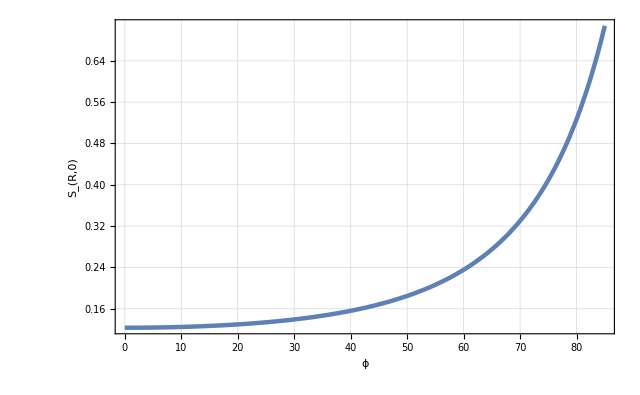

Stokes Vector R.

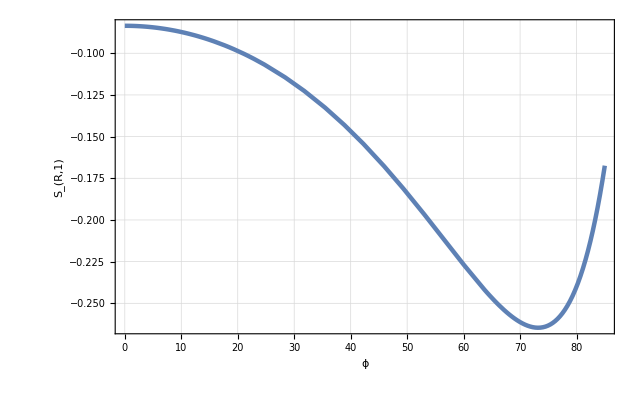

Stokes Vector R.

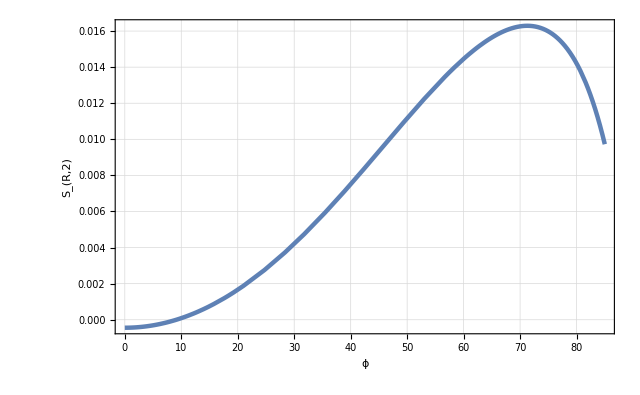

Stokes Vector R.

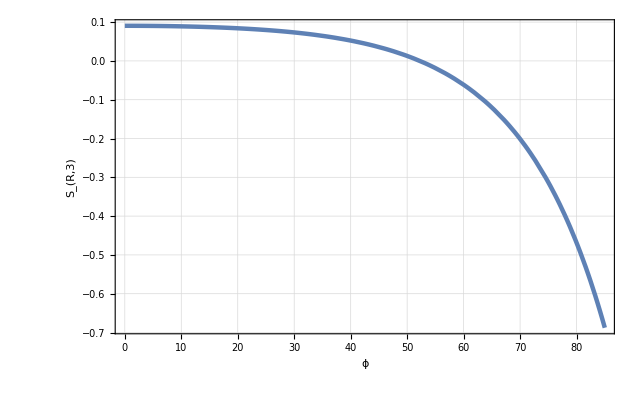

Full intensity of Reflected light.

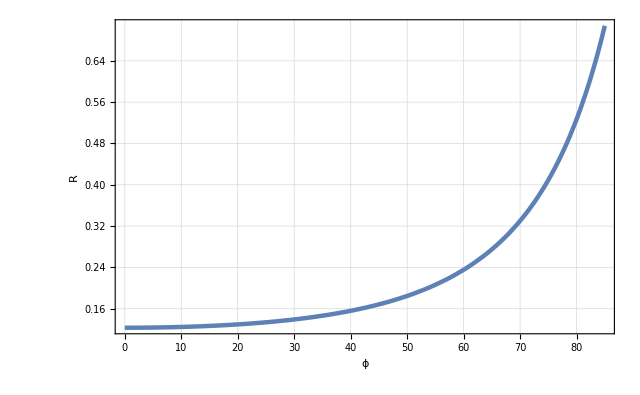

Full intensity of Transmitted light.

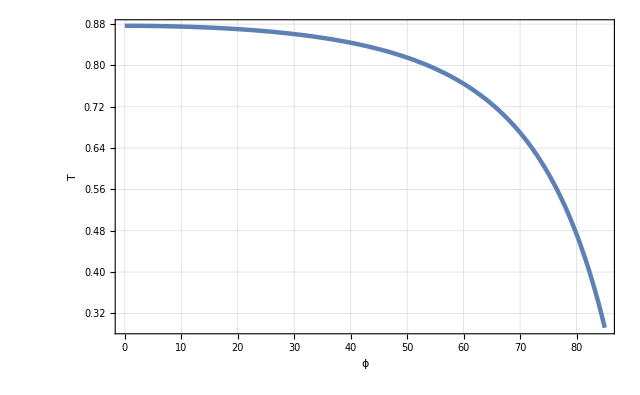

γ of Stokes Vector R.

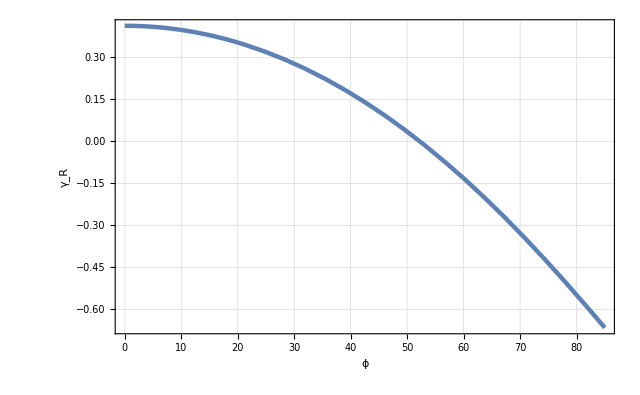

γ of Stokes Vector R (in degrees).

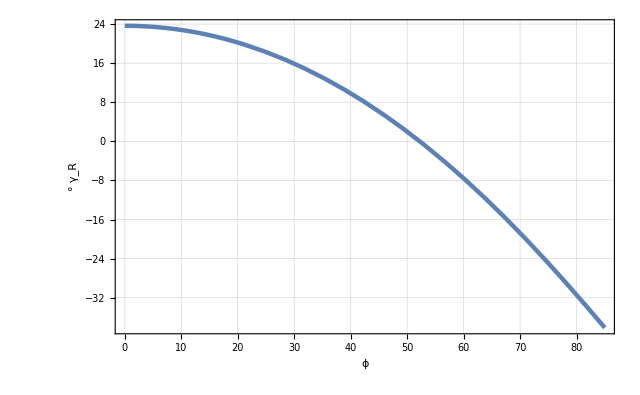

χ of Stokes Vector R.

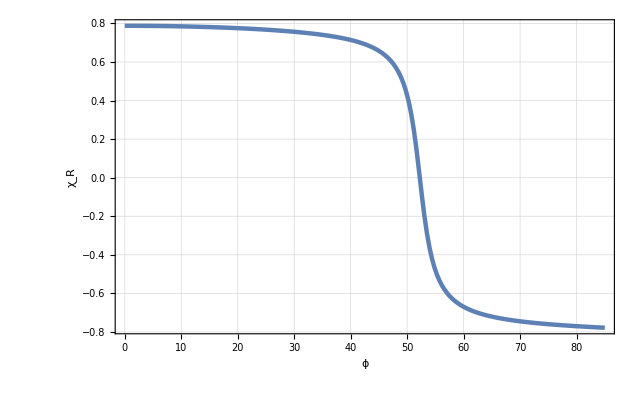

χ of Stokes Vector R (in degrees).

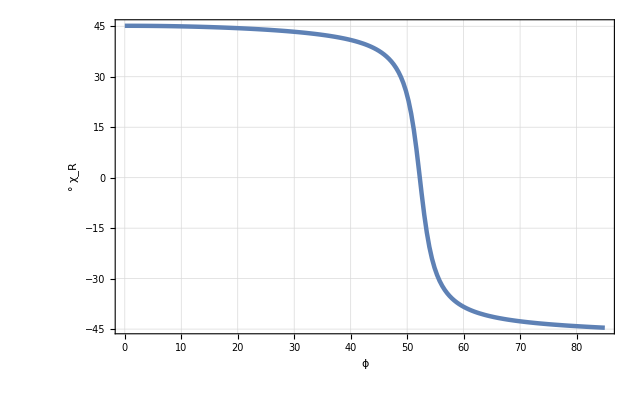

p of Stokes Vector R.

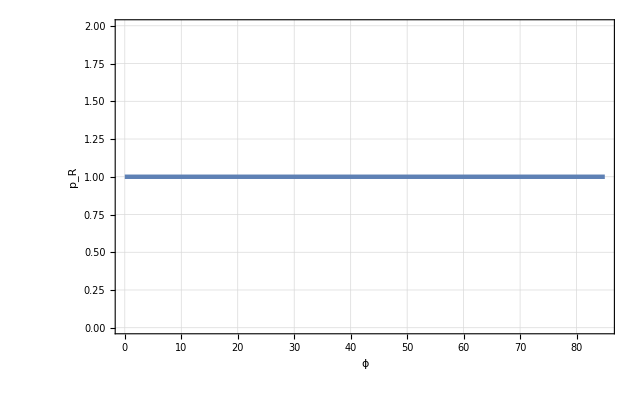

Azimuth of Reflected light in Degrees (new).

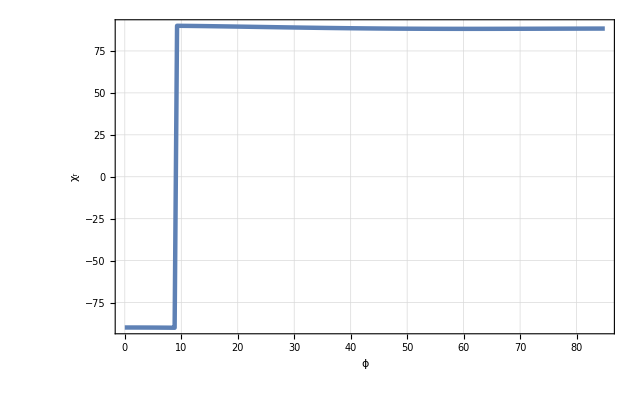

Ellipticity of Reflected light (new).

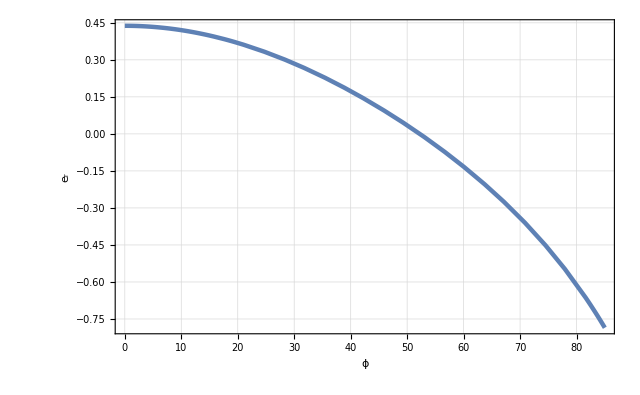

Psi pp in degrees.

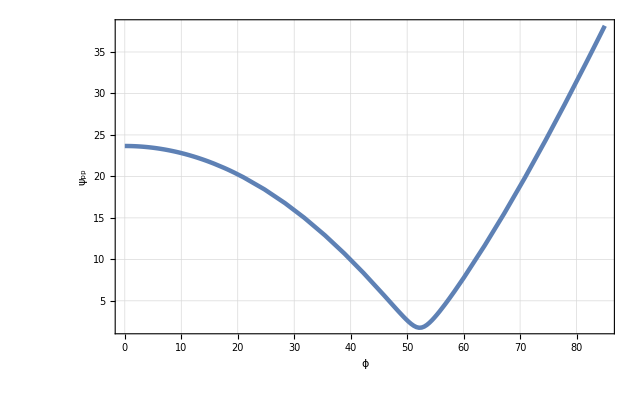

Delta pp in degrees.

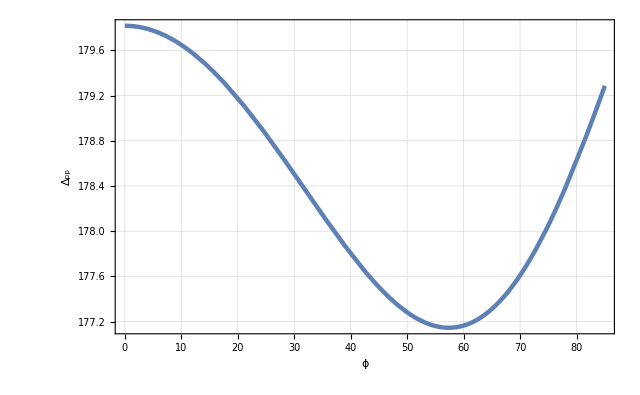

{Intensity of Reflected light going into X component.,Intensity of Reflected light going into Y component.}

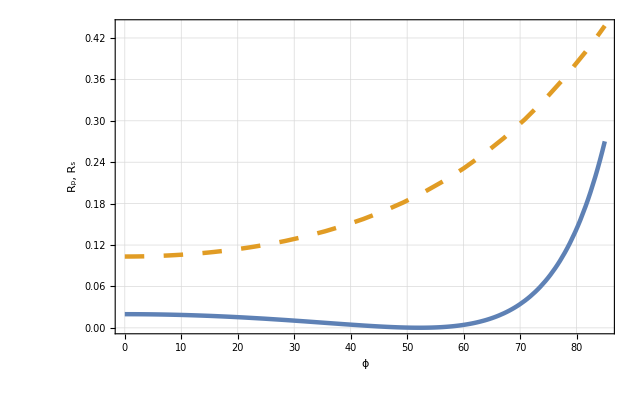

{Intensity of Transmitted light going into X component.,Intensity of Transmitted light going into Y component.}

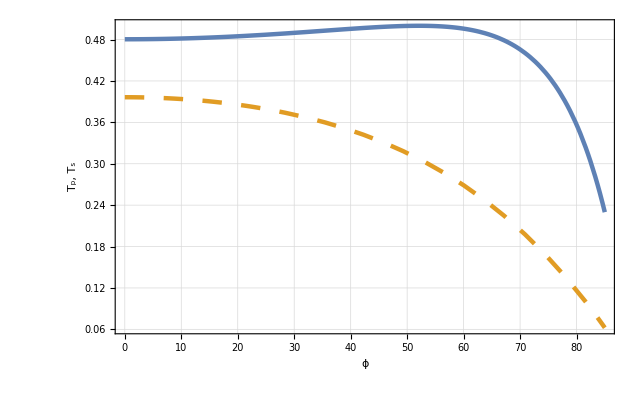

Wed 13 Apr 2016 00:42:07, time used: 183, total time used: 185.
---------------------------------------------

```mathematica
(* ============================================== *)
ClearAll["Global`*"];
(* ============================================== *)
PathList={"W:\\Math\\BM\\"};
BaseDir="W:\\Math\\BM\\";
BaseFileName="Example_06a";
OutDir=BaseDir <>"Calc\\";
(* ============================================== *)
useParallelTbl=False;
Get["BerremanInit.m",Path-> PathList];
Initialize[PathList, useParallelTbl];
(* ============================================== *)
opts={BDPlotFigures -> True,UseEulerAngles->False};
(* ============================================== *)
(*
FuncList={{StokesVectorI[1],StokesVectorI[2],StokesVectorI[3],StokesVectorI[4]},{StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4]},{EltEG[1],EltEG[2],EltEG[3],EltEG[4]},{XitEGDegree[1],XitEGDegree[2],XitEGDegree[3],XitEGDegree[4]},{IFull,RFull,TFull},{Ix,Iy,Rx,Ry,Tx,Ty},{Eli,Elr,Elt},{XiiDegree, XirDegree,XitDegree},{Sin2Xii,Sin2Xir,Sin2Xit}};
*)

FuncList={StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4],RFull,TFull, StokesGammaR, StokesGammaDegreeR,StokesChiR, StokesChiDegreeR, StokesPolarizedR,XirDegree,Elr,PsiPPDegree,DeltaPPDegree,{Rx,Ry},{Tx,Ty}};

(* ============================================== *)
systemDescription="One Layer biaxial optically active thin film between two semi-infinite media.";
(* ============================================== *)
Print["Параметры падающего света..."];
nUpper=1; 

lambda={600,600,1,"λ",nm};fita={0,85,85,"ϕ", Degree};beta={0,0,30,"β", Degree};gamma={0, 0,30,"γ",Degree};
ellipt={-1,1,0.5,"e"};

incidentLight=CreateIncidentRay[nUpper,lambda,fita,beta, ellipt];
OutputIncidentRayInfo[incidentLight];
(* ============================================== *)
Print["Оптические параметры первого тонкого слоя."];
thicknessLayer1={75,75,10,"h",nm};

fiLayer1={0, 0, 30,Subscript["φ","1"], Degree};thetaLayer1={0,0,30,Subscript["θ","1"],Degree};psiLayer1={0,0,30,Subscript["ψ","1"], Degree};
rotationAnglesLayer1={fiLayer1,thetaLayer1,psiLayer1};

epsLayer1=EpsilonFromN[1.50,2.00,1.75];
muLayer1=DiagonalMatrix[{1,1,1}];
rhoLayer1=I*{{1.9*10^-3,-3.5*10^-3,0},{3.5*10^-3,1.9*10^-3,0},{0,0,-5.7*10^-3}};

Print["epsLayer1 = ", epsLayer1 // MatrixForm];
Print["muLayer1 = ", muLayer1 // MatrixForm];
Print["rhoLayer1 = ", rhoLayer1 // MatrixForm];

layer1=CreateFilm[thicknessLayer1,rotationAnglesLayer1,epsLayer1,muLayer1,rhoLayer1];
(* ============================================== *)
Print["Оптические параметры нижней среды..."];
nLower=1.5;
lowerMedia=CreateSemiInfiniteMediaFromN[nLower];
(* ============================================== *)
Print["Создаем оптическую систему..."];
layeredSystem = CreateLayeredSystem[incidentLight,gamma,layer1,lowerMedia];
OutputLayeredSystem[layeredSystem];
(* ============================================== *)
Print["Производим вычисления для различных значений параметров...."];
allCalc=PerformAllCalculations[layeredSystem,FuncList, systemDescription,opts];
(* ============================================== *)
```